```mathematica
{y+(g x^2 Sec[θ]^2)/(2 v^2)==x Tan[θ]}~Solve~v
```

{{v→-(√g x Sec[θ])/(√2 √(-y+x Tan[θ]))},{v→(√g x Sec[θ])/(√2 √(-y+x Tan[θ]))}}

```mathematica
x=1000;
y=50;
g=98/10;
Minimize[{(Sqrt[g] x Sec[θ])/(Sqrt[2] Sqrt[-y+x Tan[θ]]),0<θ<Pi/2},θ]//FullSimplify//ToRadicals
%//N
```

{7 √(10 (1+√401)),{θ→2 ArcTan[1/20 (1-√401+√(2 (401-√401)))]}}

{101.5,{θ→0.810377}}

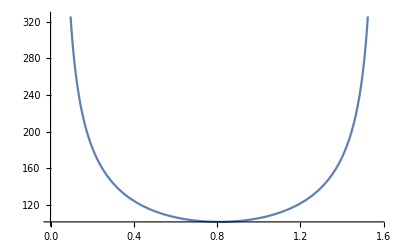

```mathematica
Plot[(Sqrt[g] x Sec[θ])/(Sqrt[2] Sqrt[-y+x Tan[θ]]),{θ,0,Pi/2}]
```